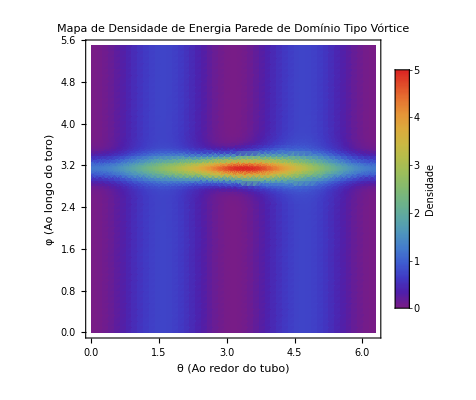

-Graphics3D-

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

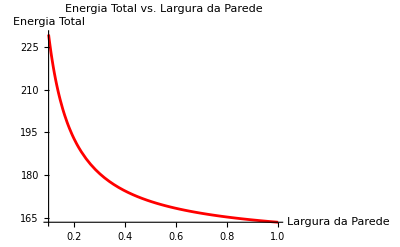

```mathematica
(*Parâmetros geométricos do toro*)R=3; (*Raio maior*)
r=1; (*Raio menor*)
A=1; (*Constante de troca,normalizada para 1*)
openingAngle=π/4; (*Ângulo da abertura no toro*)

(*Parametrização do toro com abertura*)
(*O parâmetro φ agora vai de 0 a 2π-openingAngle*)
torusX[θ_,φ_]:=(R+r*Cos[θ])*Cos[φ]
torusY[θ_,φ_]:=(R+r*Cos[θ])*Sin[φ]
torusZ[θ_,φ_]:=r*Sin[θ]

(*Funções para a configuração de magnetização de uma parede de domínio tipo vórtice*)
(*Theta é o ângulo polar (fora do plano) e Psi é o ângulo azimutal (no plano)*)

(*Função para criar uma parede de domínio tipo vórtice ao redor do toro*)
(*A parede de domínio está em uma posição específica ao redor do toro (no ângulo φ)*)
vortexWallTheta[θ_,φ_,wallPos_,wallWidth_]:=π/2 (*Magnetização se mantém no plano-tipo vórtice*)

(*Função para o ângulo azimutal-define a rotação ao redor do tubo*)
(*Para um vórtice,a magnetização circula ao redor do tubo*)
vortexWallPsi[θ_,φ_,wallPos_,wallWidth_]:=θ+π/2*Tanh[(φ-wallPos)/wallWidth] (*Circula ao redor do tubo com transição na wallPos*)

(*Derivadas parciais de Theta em relação a θ e φ*)
DvortexWallTheta[θ_,φ_,wallPos_,wallWidth_]:={0,0}

(*Derivadas parciais de Psi em relação a θ e φ*)
DvortexWallPsi[θ_,φ_,wallPos_,wallWidth_]:={1,(π/2)*(1/wallWidth)*(1/Cosh[(φ-wallPos)/wallWidth]^2)}

(*Densidade de energia de troca para a configuração de vórtice*)
vortexExchangeEnergy[θ_,φ_,wallPos_,wallWidth_]:=A*((*Termos de Theta-magnetização no plano*)1/r^2*DvortexWallTheta[θ,φ,wallPos,wallWidth][[1]]^2+1/(R+r*Cos[θ])^2*DvortexWallTheta[θ,φ,wallPos,wallWidth][[2]]^2-(2*Sin[θ])/(R+r*Cos[θ])*DvortexWallTheta[θ,φ,wallPos,wallWidth][[2]]+Sin[θ]^2+(*Termos de Psi-rotação no plano*)Sin[vortexWallTheta[θ,φ,wallPos,wallWidth]]^2*(1/r^2*DvortexWallPsi[θ,φ,wallPos,wallWidth][[1]]^2+1/(R+r*Cos[θ])^2*(DvortexWallPsi[θ,φ,wallPos,wallWidth][[2]]-r*Sin[θ]/(R+r*Cos[θ]))^2))

(*Função para desenhar vetores de magnetização no toro*)
magnetizationVector[θ_,φ_,wallPos_,wallWidth_]:=Module[{th=vortexWallTheta[θ,φ,wallPos,wallWidth],ps=vortexWallPsi[θ,φ,wallPos,wallWidth],pos,tangent,normal,binormal,mag},(*Posição no toro*)pos={torusX[θ,φ],torusY[θ,φ],torusZ[θ,φ]};
(*Vetores base locais no toro*)tangent=Normalize[{-r*Sin[θ]*Cos[φ],-r*Sin[θ]*Sin[φ],r*Cos[θ]}];(*Tangente à seção transversal*)binormal=Normalize[{-(R+r*Cos[θ])*Sin[φ],(R+r*Cos[θ])*Cos[φ],0}];(*Tangente ao círculo maior*)normal=Normalize[Cross[tangent,binormal]];(*Normal à superfície*)(*Vetor de magnetização em coordenadas locais*)mag=Sin[th]*Cos[ps]*tangent+Sin[th]*Sin[ps]*binormal+Cos[th]*normal;
(*Retorna a posição e o vetor de magnetização*){pos,0.2*mag}]

(*Interface interativa para visualizar a parede de domínio tipo vórtice no toro aberto*)
Manipulate[DynamicModule[{energyPlot,vectorPlot},(*Plot da densidade de energia*)energyPlot=ParametricPlot3D[{torusX[θ,φ],torusY[θ,φ],torusZ[θ,φ]},{θ,0,2π},{φ,0,2π-openingAngle},PlotStyle->Directive[Opacity[0.7]],Mesh->{12,Round[12*(2π-openingAngle)/2π]},PlotPoints->40,ColorFunction->Function[{x,y,z,θ,φ},ColorData["Rainbow"][Rescale[vortexExchangeEnergy[θ,φ,wallPos,wallWidth],{0,5}]]],ColorFunctionScaling->False,PlotLabel->"Densidade de Energia de Troca\nParede de Domínio Tipo Vórtice",AxesLabel->{"X","Y","Z"},Boxed->False,Lighting->"Neutral"];
(*Vetores de magnetização*)If[showVectors,(*Calcular posições e vetores de magnetização em pontos amostrais*)vectorPoints=Flatten[Table[magnetizationVector[θ,φ,wallPos,wallWidth],{θ,0,2π,2π/10},{φ,0,2π-openingAngle,(2π-openingAngle)/12}],1];
(*Adicionar os vetores ao gráfico*)vectorPlot=Graphics3D[{Red,Arrowheads[0.02],Arrow[{#[[1]],#[[1]]+#[[2]]}]&/@vectorPoints}];
Show[energyPlot,vectorPlot,PlotRange->All],(*Sem vetores*)energyPlot]],(*Controles para os parâmetros*){{R,3,"Raio Maior (R)"},2,5,0.1,Appearance->"Labeled"},{{r,1,"Raio Menor (r)"},0.5,1.5,0.1,Appearance->"Labeled"},{{openingAngle,π/4,"Ângulo da Abertura"},0,π/2,π/20,Appearance->"Labeled"},{{wallPos,π,"Posição da Parede"},0,2π-π/4,0.1,Appearance->"Labeled"},{{wallWidth,0.3,"Largura da Parede"},0.1,1,0.1,Appearance->"Labeled"},{{showVectors,True,"Mostrar Vetores"},{True,False}},ControlPlacement->Left]

(*Visualização do campo de energia em coordenadas paramétricas*)
DensityPlot[vortexExchangeEnergy[θ,φ,π,0.3],{θ,0,2π},{φ,0,2π-π/4},PlotRange->All,PlotPoints->50,ColorFunction->"Rainbow",FrameLabel->{"θ (Ao redor do tubo)","φ (Ao longo do toro)"},PlotLabel->"Mapa de Densidade de Energia\nParede de Domínio Tipo Vórtice",PlotLegends->BarLegend[{"Rainbow",{0,5}},LegendLabel->"Densidade"]]

(*Gráfico 3D da densidade de energia como uma função de altura*)
Plot3D[vortexExchangeEnergy[θ,φ,π,0.3],{θ,0,2π},{φ,0,2π-π/4},PlotRange->{0,5},PlotPoints->50,ColorFunction->"Rainbow",AxesLabel->{"θ","φ","Energia"},BoxRatios->{1,(2π-π/4)/(2π),0.5},PlotLabel->"Superfície da Densidade de Energia\nParede de Domínio Tipo Vórtice"]

(*Cálculo da energia total integrada sobre o toro*)
totalEnergy[wallPos_,wallWidth_]:=NIntegrate[vortexExchangeEnergy[θ,φ,wallPos,wallWidth]*r*(R+r*Cos[θ]),{θ,0,2π},{φ,0,2π-π/4}]

(*Plotar a energia total em função da largura da parede*)
Plot[totalEnergy[π,width],{width,0.1,1},PlotRange->All,AxesLabel->{"Largura da Parede","Energia Total"},PlotLabel->"Energia Total vs. Largura da Parede",PlotStyle->Red]
```

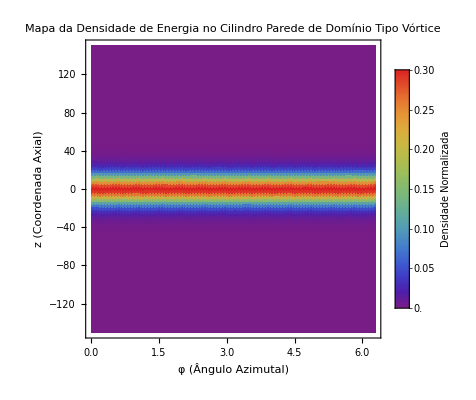

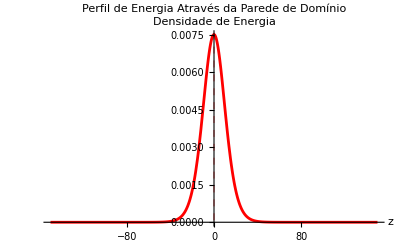

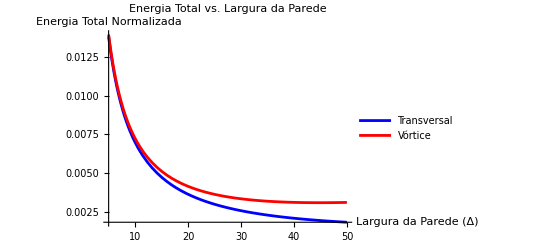

```mathematica
(*Parâmetros geométricos do cilindro*)R=100; (*Raio do cilindro*)
L=300; (*Comprimento do cilindro*)
β=0.2; (*Parâmetro relacionado à razão de aspecto*)
s=1; (*Constante relacionada à espessura da casca magnética*)
A=1; (*Constante de troca,normalizada*)

(*Parametrização do cilindro*)
cylinderX[φ_,z_]:=R*Cos[φ]
cylinderY[φ_,z_]:=R*Sin[φ]
cylinderZ[φ_,z_]:=z

(*Funções para a configuração de magnetização de uma parede de domínio tipo vórtice*)
(*Theta é o ângulo polar (fora do plano) e Psi é o ângulo azimutal (no plano)*)

(*Configuração para uma parede de domínio transversal no cilindro*)
(*A parede está localizada em z0 com largura delta*)
domainWallTheta[φ_,z_,z0_,delta_]:=π/2*(1+Tanh[(z-z0)/delta])
DdomainWallTheta[φ_,z_,z0_,delta_]:={0,(*∂φΘ*)(π/2)*(1/delta)*(1/Cosh[(z-z0)/delta]^2) (*∂zΘ*)}

(*Configuração para o ângulo azimutal-vórtice ou não-vórtice*)
domainWallPsi[φ_,z_,z0_,delta_,vorticity_]:=vorticity*φ
DdomainWallPsi[φ_,z_,z0_,delta_,vorticity_]:={vorticity,(*∂φΨ*)0 (*∂zΨ*)}

(*Densidade de energia de troca para o cilindro usando a expressão fornecida*)
cylinderExchangeEnergy[φ_,z_,z0_,delta_,vorticity_]:=(2*π*s*A)*((*Termo (∂zΘ).b2*)DdomainWallTheta[φ,z,z0,delta][[2]]^2+(*Termo sin.b2Θ(∂zΨ).b2*)Sin[domainWallTheta[φ,z,z0,delta]]^2*DdomainWallPsi[φ,z,z0,delta,vorticity][[2]]^2+(*Termo (2log(1/β))/(R.b2(1-β.b2))*[(∂φΘ).b2+sin.b2Θ(1+∂φΨ).b2]*)(2*Log[1/β])/(R^2*(1-β^2))*(DdomainWallTheta[φ,z,z0,delta][[1]]^2+Sin[domainWallTheta[φ,z,z0,delta]]^2*(1+DdomainWallPsi[φ,z,z0,delta,vorticity][[1]])^2))

(*Energia total integrada sobre o cilindro*)
totalEnergy[z0_,delta_,vorticity_]:=NIntegrate[cylinderExchangeEnergy[φ,z,z0,delta,vorticity]*R,{φ,0,2π},{z,-L/2,L/2}]

(*Interface interativa para visualizar a densidade de energia no cilindro*)
Manipulate[DynamicModule[{energyPlot,vectorPlot,maxEnergy},(*Calcular o valor máximo de energia para normalização*)maxEnergy=5*(π/2)^2*(1/delta)^2;(*Estimativa baseada no termo dominante próximo à parede*)(*Plot da densidade de energia*)energyPlot=ParametricPlot3D[{cylinderX[φ,z],cylinderY[φ,z],cylinderZ[φ,z]},{φ,0,2π},{z,-L/2,L/2},PlotStyle->Directive[Opacity[0.7]],Mesh->{12,24},PlotPoints->50,ColorFunction->Function[{x,y,z,φ,zz},ColorData["Rainbow"][Rescale[cylinderExchangeEnergy[φ,zz,z0,delta,vorticity],{0,maxEnergy}]]],ColorFunctionScaling->False,PlotLabel->"Densidade de Energia de Troca no Cilindro\nParede de Domínio Tipo "<>If[vorticity==0,"Transversal","Vórtice"],AxesLabel->{"X","Y","Z"},Boxed->False,Lighting->"Neutral"];
(*Vetores de magnetização*)If[showVectors,(*Gerar pontos amostrais para os vetores*)vectorPoints=Flatten[Table[Module[{pos,theta,psi,mx,my,mz},(*Posição no cilindro*)pos={cylinderX[φ,z],cylinderY[φ,z],cylinderZ[φ,z]};
(*Ângulos da magnetização*)theta=domainWallTheta[φ,z,z0,delta];
psi=domainWallPsi[φ,z,z0,delta,vorticity];
(*Componentes da magnetização*)mx=Sin[theta]*Cos[psi];
my=Sin[theta]*Sin[psi];
mz=Cos[theta];
(*Vetor de magnetização no sistema de coordenadas do cilindro*){pos,20*{mx*Cos[φ]-my*Sin[φ],mx*Sin[φ]+my*Cos[φ],mz}}],{φ,0,2π,2π/8},{z,-L/2,L/2,L/8}],1];
(*Criar gráfico de vetores*)vectorPlot=Graphics3D[{Red,Arrowheads[0.02],Arrow[{#[[1]],#[[1]]+#[[2]]}]&/@vectorPoints}];
Show[energyPlot,vectorPlot,PlotRange->All],(*Sem vetores*)energyPlot]],(*Controles para os parâmetros*){{R,100,"Raio do Cilindro (R)"},50,150,10,Appearance->"Labeled"},{{L,300,"Comprimento do Cilindro (L)"},200,500,50,Appearance->"Labeled"},{{β,0.2,"Parâmetro β"},0.1,0.5,0.05,Appearance->"Labeled"},{{z0,0,"Posição da Parede (z₀)"},-L/2,L/2,L/20,Appearance->"Labeled"},{{delta,20,"Largura da Parede (Δ)"},5,50,5,Appearance->"Labeled"},{{vorticity,1,"Tipo de Parede"},{0->"Transversal",1->"Vórtice"}},{{showVectors,True,"Mostrar Vetores"},{True,False}},ControlPlacement->Left]

(*Visualização em mapa de densidade*)
DensityPlot[cylinderExchangeEnergy[φ,z,0,20,1]/((2*π*s*A)),(*Normalizado*){φ,0,2π},{z,-L/2,L/2},PlotRange->All,PlotPoints->100,ColorFunction->"Rainbow",FrameLabel->{"φ (Ângulo Azimutal)","z (Coordenada Axial)"},PlotLabel->"Mapa da Densidade de Energia no Cilindro\nParede de Domínio Tipo Vórtice",PlotLegends->BarLegend[{"Rainbow",{0,0.3}},LegendLabel->"Densidade Normalizada"]]

(*Perfil de energia através da parede de domínio*)
Plot[cylinderExchangeEnergy[0,z,0,20,1]/((2*π*s*A)),(*Valor em φ=0,normalizado*){z,-L/2,L/2},PlotRange->All,AxesLabel->{"z","Densidade de Energia"},PlotStyle->Red,PlotLabel->"Perfil de Energia Através da Parede de Domínio",GridLines->{{0},None},GridLinesStyle->Directive[Red,Dashed]]

(*Energia total vs largura da parede para diferentes tipos de paredes*)
Plot[{totalEnergy[0,delta,0]/(2*π*s*A*R*L),(*Parede transversal,normalizada*)totalEnergy[0,delta,1]/(2*π*s*A*R*L)  (*Parede tipo vórtice,normalizada*)},{delta,5,50},PlotRange->All,AxesLabel->{"Largura da Parede (Δ)","Energia Total Normalizada"},PlotLabel->"Energia Total vs. Largura da Parede",PlotStyle->{Blue,Red},PlotLegends->{"Transversal","Vórtice"}]
```

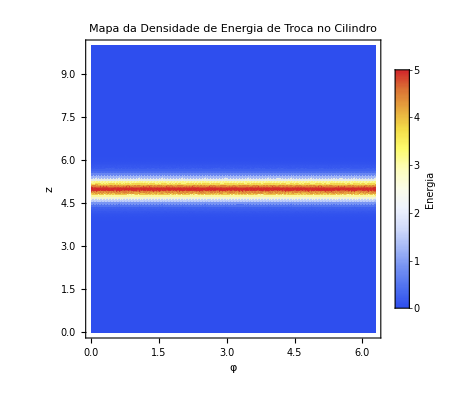

```mathematica
(*Parâmetros geométricos do cilindro*)r=1;       (*Raio do cilindro*)
L=10;      (*Comprimento do cilindro*)
A=1;       (*Constante de troca,normalizada*)
beta=0.2;  (*Parâmetro relacionado à geometria*)

(*Parametrização do cilindro*)
cylinderX[φ_,z_]:=r*Cos[φ]
cylinderY[φ_,z_]:=r*Sin[φ]
cylinderZ[φ_,z_]:=z

(*Configuração de magnetização*)
Theta[φ_,z_]:=π/2*(1+Tanh[(z-L/2)/0.5])
Phi[φ_,z_]:=φ

(*Derivadas parciais*)
dThetadPhi[φ_,z_]:=D[Theta[p,z],p]/. p->φ
dThetadZ[φ_,z_]:=D[Theta[φ,t],t]/. t->z

dPhidPhi[φ_,z_]:=D[Phi[p,z],p]/. p->φ
dPhidZ[φ_,z_]:=D[Phi[φ,t],t]/. t->z

(*Densidade de energia de troca para o cilindro*)
cylinderExchangeEnergy[φ_,z_]:=(dThetadZ[φ,z])^2+Sin[Theta[φ,z]]^2*(dPhidZ[φ,z])^2+(2*Log[1/beta])/(r^2*(1-beta^2))*((dThetadPhi[φ,z])^2+Sin[Theta[φ,z]]^2*(1+dPhidPhi[φ,z])^2)

(*Visualização do cilindro com a densidade de energia mapeada*)
Manipulate[Module[{maxEnergy=5},Show[ParametricPlot3D[{cylinderX[φ,z],cylinderY[φ,z],cylinderZ[φ,z]},{φ,0,2π},{z,0,L},PlotPoints->50,Mesh->{15,15},ColorFunction->Function[{x,y,z,u,v},ColorData["TemperatureMap"][Min[1,cylinderExchangeEnergy[u,v]/maxEnergy]]],ColorFunctionScaling->False,PlotLabel->"Densidade de Energia de Troca no Cilindro",Boxed->False,Axes->False,Lighting->"Neutral"]]],{{r,1,"Raio do Cilindro"},0.5,2,0.1},{{L,10,"Comprimento do Cilindro"},5,15,1},{{beta,0.2,"Parâmetro β"},0.1,0.5,0.05},ControlPlacement->Left]

(*Mapa de densidade de energia do cilindro*)
DensityPlot[cylinderExchangeEnergy[φ,z],{φ,0,2π},{z,0,L},PlotRange->All,PlotPoints->100,ColorFunction->"TemperatureMap",FrameLabel->{"φ","z"},PlotLabel->"Mapa da Densidade de Energia de Troca no Cilindro",PlotLegends->BarLegend[{"TemperatureMap",{0,5}},LegendLabel->"Energia"]]
```

```mathematica
(*Adicionando a visualização 3D da densidade de energia para o cilindro*)Plot3D[cylinderExchangeEnergy[φ,z],{φ,0,2π},{z,0,L},PlotRange->{0,5},PlotPoints->50,ColorFunction->"TemperatureMap",AxesLabel->{"φ","z","Energia"},BoxRatios->{2π,L,3},PlotLabel->"Superfície 3D da Densidade de Energia no Cilindro"]

(*Visualização combinada:Cilindro com a superfície de energia*)
Module[{maxEnergy=5,scale=0.3},Show[(*Cilindro*)ParametricPlot3D[{cylinderX[φ,z],cylinderY[φ,z],cylinderZ[φ,z]},{φ,0,2π},{z,0,L},PlotStyle->Directive[Opacity[0.7],LightGray],Mesh->{10,10},PlotPoints->30],(*Superfície de energia-projetada para fora do cilindro*)ParametricPlot3D[{(r+scale*cylinderExchangeEnergy[φ,z])*Cos[φ],(r+scale*cylinderExchangeEnergy[φ,z])*Sin[φ],z},{φ,0,2π},{z,0,L},PlotStyle->Directive[Opacity[0.7]],ColorFunction->Function[{x,y,z,u,v},ColorData["TemperatureMap"][Min[1,cylinderExchangeEnergy[u,v]/maxEnergy]]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50],PlotRange->All,Boxed->False,Axes->False,Lighting->"Neutral",PlotLabel->"Energia de Troca Projetada no Cilindro"]]
```

-Graphics3D-

-Graphics3D-